## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="G3PD2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_G3PD2_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | glyc3p | nadp | 0.000099 | 0.00009405
0.00010395 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadph | 3.4×10^-6 | 3.23×10^-6
3.57×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | dhap | 0.00018 | 0.000171
0.000189 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | nadp | 0.000165 | 0.00015675
0.00017325 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | glyc3p | 0.00003 | 0.0000285
0.0000315 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | glyc3p | 4.2×10^-6 | 3.99×10^-6
4.41×10^-6 | nadph | 0.0001 | Competitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | glyc3p | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | glyc3p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadp | 0.000187 | 0.00017765
0.00019635 | dhap | 0.002 | Competitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | dhap | 0.000038 | 0.0000361
0.0000399 | nadp | 0.002 | Competitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | dhap | 0.00024 | 0.000228
0.000252 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | dhap | 0.00012 | 0.000114
0.000126 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadph | 8.×10^-7 | 7.6×10^-7
8.4×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadph | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadph | 4.×10^-7 | 3.8×10^-7
4.2×10^-7 | glyc3p | 0.0002 | Competitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1};
s05Priorities = Null;
kcatPriorities = Null;
inhibitionPriorities={1,1,1, 1,1,1,1,1,1,1,1,1};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | glyc3p | nadp | 0.000099 | 0.00009405
0.00010395 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadph | 3.4×10^-6 | 3.23×10^-6
3.57×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | dhap | 0.00018 | 0.000171
0.000189 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | nadp | 0.000165 | 0.00015675
0.00017325 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | glyc3p | 0.00003 | 0.0000285
0.0000315 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | glyc3p | 4.2×10^-6 | 3.99×10^-6
4.41×10^-6 | nadph | 0.0001 | Competitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | glyc3p | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | glyc3p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadp | 0.000187 | 0.00017765
0.00019635 | dhap | 0.002 | Competitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | dhap | 0.000038 | 0.0000361
0.0000399 | nadp | 0.002 | Competitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | dhap | 0.00024 | 0.000228
0.000252 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | dhap | 0.00012 | 0.000114
0.000126 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadph | 8.×10^-7 | 7.6×10^-7
8.4×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadph | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadph | 4.×10^-7 | 3.8×10^-7
4.2×10^-7 | glyc3p | 0.0002 | Competitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_G3PD2[c] + nadp[c] <=> E_G3PD2[c]&nadp",
				"E_G3PD2[c]&nadp + glyc3p[c] <=> E_G3PD2[c]&nadp&glyc3p",
				"E_G3PD2[c]&nadp&glyc3p <=> E_G3PD2[c]&nadph&dhap",
				"E_G3PD2[c]&nadph&dhap <=> E_G3PD2[c]&nadph + dhap[c]",
				"E_G3PD2[c]&nadph <=> E_G3PD2[c] + nadph[c]"};


enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites-> 0];
enzymeModel["Reactions"]
```

enzymeModel[Reactions]

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,Overscript[(G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c, G3PD22],((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,Overscript[(G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c, G3PD24],((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={{"prod_inhib_dhap", nadph^c->0},{ "prod_inhib_nadph", dhap^c->0}};
otherMetsForwardZeroSub={{"prod_inhib_glyc3p", nadp^c->0},{"prod_inhib_nadp", glyc3p^c->0}};
inhibitionListSubset=inhibitionList[[{2,3,8,9}]];


{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionListSubset, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

prod inhib

Generating flux equation...

{((G3PD2^c&nadp^c&glyc3p^c)_^-((G3PD2^c&nadph^c&dhap^c)_^)/K_G3PD25) Volume_c k_G3PD25^⟶}

Volume_c (-(G3PD2^c&nadph^c&dhap^c)_^ k_G3PD25^⟵+(G3PD2^c&nadp^c&glyc3p^c)_^ k_G3PD25^⟶)

Simplifying...

Added inhibition reactions:

{((G3PD2^c&nadph^c)_^+glyc3p^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_Kincu_glyc3p_1_nadph,((G3PD2^c)_^+glyc3p^c⇌(G3PD2^c&glyc3p^c)_^)^G3PD2_Kincc_glyc3p_1_nadph,((G3PD2^c&glyc3p^c)_^+nadph^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_NC_glyc3p,((G3PD2^c&nadp^c)_^+dhap^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_Kincu_dhap_1_nadp,((G3PD2^c)_^+dhap^c⇌(G3PD2^c&dhap^c)_^)^G3PD2_Kincc_dhap_1_nadp,((G3PD2^c&dhap^c)_^+nadp^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_NC_dhap}

Generating flux equation...

{((G3PD2^c&nadp^c&glyc3p^c)_^-((G3PD2^c&nadph^c&dhap^c)_^)/K_G3PD25) Volume_c k_G3PD25^⟶}

Volume_c (-(G3PD2^c&nadph^c&dhap^c)_^ k_G3PD25^⟵+(G3PD2^c&nadp^c&glyc3p^c)_^ k_G3PD25^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating other relative rate forward equation...

Simplifying...

Generating other relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	glyc3p[c]	nadp[c]	nadph[c]	param_G3PD2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	1	0	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.09090909090909097
1	1	0	0	5.388636854367791e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.1368068886032101
1	1	0	0	8.540413867132584e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.20076000891310194
1	1	0	0	1.3535643798818904e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.2847472489508014
1	1	0	0	2.1452549712326573e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.386863179846857
1	1	0	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.5000000000000001
1	1	0	0	5.388636854367791e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.6131368201531433
1	1	0	0	8.540413867132584e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.7152527510491989
1	1	0	0	0.000013535643798818902	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.7992399910868982
1	1	0	0	0.000021452549712326573	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.86319311139679
1	1	0	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.9090909090909091
1	0.000018000000000000017	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.09090909090909098
1	0.00002852807746430008	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.13680688860321016
1	0.00004521395576717252	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.200760008913102
1	0.00007165929069962952	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.28474724895080145
1	0.00011357232200643484	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.38686317984685703
1	0.00018000000000000017	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.5000000000000002
1	0.0002852807746430008	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.6131368201531433
1	0.0004521395576717252	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.7152527510491989
1	0.0007165929069962958	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.7992399910868984
1	0.0011357232200643484	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.86319311139679
1	0.0018000000000000017	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.9090909090909092
1	0	1	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.09090909090909097
1	0	1	0.000026150737675608408	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.13680688860321016
1	0	1	0.000041446126119908146	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.20076000891310203
1	0	1	0.00006568768314132706	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.2847472489508014
1	0	1	0.00010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.3868631798468571
1	0	1	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.5000000000000002
1	0	1	0.0002615073767560841	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.6131368201531434
1	0	1	0.0004144612611990815	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.7152527510491989
1	0	1	0.0006568768314132713	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.7992399910868985
1	0	1	0.0010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.8631931113967901
1	0	1	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.9090909090909092
1	0	3.0000000000000013e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.09090909090909094
1	0	4.7546795773833446e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.1368068886032101
1	0	7.535659294528749e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.20076000891310194
1	0	0.000011943215116604912	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.28474724895080133
1	0	0.000018928720334405797	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.3868631798468569
1	0	0.00003000000000000001	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.5000000000000001
1	0	0.00004754679577383344	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.6131368201531432
1	0	0.00007535659294528749	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.7152527510491988
1	0	0.00011943215116604925	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.7992399910868984
1	0	0.00018928720334405796	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.86319311139679
1	0	0.00030000000000000014	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.9090909090909091
1	0.000018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.06250000000000006
1	0.000056920997883030876	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.17411239489546845
1	0.00018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.4000000000000002
1	0.0005692099788303088	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6782688399674107
1	0.0018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8695652173913044
1	0.000018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.047619047619047665
1	0.000056920997883030876	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.13652705949581442
1	0.00018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.33333333333333354
1	0.0005692099788303088	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6125741132772071
1	0.0018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8333333333333335
1	0.000018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.032258064516129066
1	0.000056920997883030876	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.09535767393826004
1	0.00018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.2500000000000002
1	0.0005692099788303088	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.5131670194948622
1	0.0018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.7692307692307694
1	0.0001	2.25e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.04914933837429115
1	0.0001	2.25e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.1359715179829786
1	0.0001	2.25e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3080568720379148
1	0.0001	2.25e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5136142175737065
1	0.0001	2.25e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.6509764646970455
1	0.0001	4.5e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.03367875647668395
1	0.0001	4.5e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.09481652165128764
1	0.0001	4.5e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.22260273972602748
1	0.0001	4.5e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3879359014999326
1	0.0001	4.5e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5070202808112324
1	0.0001	9.e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.0206677265500795
1	0.0001	9.e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.059062933642962216
1	0.0001	9.e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.14317180616740097
1	0.0001	9.e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.2604666499256048
1	0.0001	9.e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.351541373715522
1	0.000018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.06060606060606066
1	0.000056920997883030876	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16016871556802817
1	0.00018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.3333333333333335
1	0.0005692099788303088	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.5064979510986386
1	0.0018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.6060606060606061
1	0.000018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.04545454545454549
1	0.000056920997883030876	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.12012653667602116
1	0.00018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2500000000000001
1	0.0005692099788303088	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.379873463323979
1	0.0018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.4545454545454546
1	0.000018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.03030303030303033
1	0.000056920997883030876	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.08008435778401408
1	0.00018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16666666666666674
1	0.0005692099788303088	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2532489755493193
1	0.0018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.30303030303030304
1	0.002	0	0.0000935	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.06250000000000003
1	0.002	0	0.0000935	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1741123948954684
1	0.002	0	0.0000935	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.40000000000000013
1	0.002	0	0.0000935	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.6782688399674105
1	0.002	0	0.0000935	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8695652173913044
1	0.002	0	0.000187	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.047619047619047644
1	0.002	0	0.000187	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1365270594958144
1	0.002	0	0.000187	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.3333333333333334
1	0.002	0	0.000187	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.612574113277207
1	0.002	0	0.000187	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8333333333333334
1	0.002	0	0.000374	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.032258064516129045
1	0.002	0	0.000374	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.09535767393826002
1	0.002	0	0.000374	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.2500000000000001
1	0.002	0	0.000374	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.5131670194948621
1	0.002	0	0.000374	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.7692307692307694
1	0.000019	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.06250000000000003
1	0.000019	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.17411239489546837
1	0.000019	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.40000000000000013
1	0.000019	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.6782688399674105
1	0.000019	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8695652173913044
1	0.000038	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.04761904761904764
1	0.000038	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.13652705949581434
1	0.000038	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.3333333333333334
1	0.000038	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.612574113277207
1	0.000038	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8333333333333335
1	0.000076	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.032258064516129045
1	0.000076	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.09535767393826
1	0.000076	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.25000000000000006
1	0.000076	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.5131670194948622
1	0.000076	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.7692307692307693
1	0.00009	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.052980132450331174
1	0.00009	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1447390418373348
1	0.00009	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3200000000000002
1	0.00009	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.518564992170751
1	0.00009	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.6451612903225806
1	0.00018	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.03738317757009349
1	0.00018	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.10356583218373844
1	0.00018	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.235294117647059
1	0.00018	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.39361254767503817
1	0.00018	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.5000000000000001
1	0.00036	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.023529411764705903
1	0.00036	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.06601047571169773
1	0.00036	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1538461538461539
1	0.00036	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.26561052385648354
1	0.00036	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3448275862068966
1	0	3.0000000000000013e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.057901085645355864
1	0	9.486832980505141e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.15517252975139625
1	0	0.00003000000000000001	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.33103448275862074
1	0	0.00009486832980505142	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.5159442342521813
1	0	0.00030000000000000014	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.6266318537859008
1	0	3.0000000000000013e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.042477876106194704
1	0	9.486832980505141e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.11459214550830052
1	0	0.00003000000000000001	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2474226804123712
1	0	0.00009486832980505142	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.39060056309756436
1	0	0.00030000000000000014	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.47808764940239046
1	0	3.0000000000000013e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.02771362586605082
1	0	9.486832980505141e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.07523930500173176
1	0	0.00003000000000000001	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.16438356164383564
1	0	0.00009486832980505142	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2628747818212248
1	0	0.00030000000000000014	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.32432432432432434
1	0	0.0002	0.000016500000000000015	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.06250000000000006
1	0	0.0002	0.000052177581392778313	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.17411239489546848
1	0	0.0002	0.00016500000000000016	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.4000000000000002
1	0	0.0002	0.0005217758139277831	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6782688399674106
1	0	0.0002	0.0016500000000000017	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8695652173913045
1	0	0.0002	0.000016500000000000015	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.047619047619047665
1	0	0.0002	0.000052177581392778313	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.13652705949581445
1	0	0.0002	0.00016500000000000016	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.33333333333333354
1	0	0.0002	0.0005217758139277831	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6125741132772071
1	0	0.0002	0.0016500000000000017	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8333333333333335
1	0	0.0002	0.000016500000000000015	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.03225806451612906
1	0	0.0002	0.000052177581392778313	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.09535767393826007
1	0	0.0002	0.00016500000000000016	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.25000000000000017
1	0	0.0002	0.0005217758139277831	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.5131670194948623
1	0	0.0002	0.0016500000000000017	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.7692307692307693

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

```mathematica
FilePrint[dataPathList[[8]]]
```

Priority	dhap[c]	glyc3p[c]	nadp[c]	nadph[c]	param_G3PD2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000099
1	1	0	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.09090909090909097
1	1	0	0	5.388636854367791e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.1368068886032101
1	1	0	0	8.540413867132584e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.20076000891310194
1	1	0	0	1.3535643798818904e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.2847472489508014
1	1	0	0	2.1452549712326573e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.386863179846857
1	1	0	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.5000000000000001
1	1	0	0	5.388636854367791e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.6131368201531433
1	1	0	0	8.540413867132584e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.7152527510491989
1	1	0	0	0.000013535643798818902	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.7992399910868982
1	1	0	0	0.000021452549712326573	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.86319311139679
1	1	0	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.9090909090909091
1	0.000018000000000000017	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.09090909090909098
1	0.00002852807746430008	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.13680688860321016
1	0.00004521395576717252	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.200760008913102
1	0.00007165929069962952	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.28474724895080145
1	0.00011357232200643484	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.38686317984685703
1	0.00018000000000000017	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.5000000000000002
1	0.0002852807746430008	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.6131368201531433
1	0.0004521395576717252	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.7152527510491989
1	0.0007165929069962958	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.7992399910868984
1	0.0011357232200643484	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.86319311139679
1	0.0018000000000000017	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.9090909090909092
1	0	1	1.	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.09090909090909091
1	0	1	1.5848931924611136	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.13680688860321003
1	0	1	2.51188643150958	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.20076000891310172
1	0	1	3.981071705534973	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.2847472489508015
1	0	1	6.309573444801933	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.386863179846857
1	0	1	10.	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.5
1	0	1	15.848931924611142	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.6131368201531431
1	0	1	25.11886431509581	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.7152527510491987
1	0	1	39.810717055349734	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.7992399910868984
1	0	1	63.09573444801933	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.86319311139679
1	0	1	100.	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.9090909090909091
1	0	3.0000000000000013e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.09090909090909094
1	0	4.7546795773833446e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.1368068886032101
1	0	7.535659294528749e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.20076000891310194
1	0	0.000011943215116604912	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.28474724895080133
1	0	0.000018928720334405797	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.3868631798468569
1	0	0.00003000000000000001	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.5000000000000001
1	0	0.00004754679577383344	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.6131368201531432
1	0	0.00007535659294528749	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.7152527510491988
1	0	0.00011943215116604925	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.7992399910868984
1	0	0.00018928720334405796	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.86319311139679
1	0	0.00030000000000000014	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.9090909090909091
1	0.000018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.06250000000000006
1	0.000056920997883030876	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.17411239489546845
1	0.00018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.4000000000000002
1	0.0005692099788303088	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6782688399674107
1	0.0018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8695652173913044
1	0.000018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.047619047619047665
1	0.000056920997883030876	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.13652705949581442
1	0.00018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.33333333333333354
1	0.0005692099788303088	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6125741132772071
1	0.0018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8333333333333335
1	0.000018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.032258064516129066
1	0.000056920997883030876	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.09535767393826004
1	0.00018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.2500000000000002
1	0.0005692099788303088	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.5131670194948622
1	0.0018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.7692307692307694
1	0.0001	2.25e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.04914933837429115
1	0.0001	2.25e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.1359715179829786
1	0.0001	2.25e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3080568720379148
1	0.0001	2.25e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5136142175737065
1	0.0001	2.25e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.6509764646970455
1	0.0001	4.5e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.03367875647668395
1	0.0001	4.5e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.09481652165128764
1	0.0001	4.5e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.22260273972602748
1	0.0001	4.5e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3879359014999326
1	0.0001	4.5e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5070202808112324
1	0.0001	9.e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.0206677265500795
1	0.0001	9.e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.059062933642962216
1	0.0001	9.e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.14317180616740097
1	0.0001	9.e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.2604666499256048
1	0.0001	9.e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.351541373715522
1	0.000018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.06060606060606066
1	0.000056920997883030876	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16016871556802817
1	0.00018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.3333333333333335
1	0.0005692099788303088	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.5064979510986386
1	0.0018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.6060606060606061
1	0.000018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.04545454545454549
1	0.000056920997883030876	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.12012653667602116
1	0.00018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2500000000000001
1	0.0005692099788303088	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.379873463323979
1	0.0018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.4545454545454546
1	0.000018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.03030303030303033
1	0.000056920997883030876	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.08008435778401408
1	0.00018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16666666666666674
1	0.0005692099788303088	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2532489755493193
1	0.0018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.30303030303030304
1	0.002	0	0.0000935	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.06250000000000003
1	0.002	0	0.0000935	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1741123948954684
1	0.002	0	0.0000935	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.40000000000000013
1	0.002	0	0.0000935	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.6782688399674105
1	0.002	0	0.0000935	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8695652173913044
1	0.002	0	0.000187	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.047619047619047644
1	0.002	0	0.000187	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1365270594958144
1	0.002	0	0.000187	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.3333333333333334
1	0.002	0	0.000187	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.612574113277207
1	0.002	0	0.000187	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8333333333333334
1	0.002	0	0.000374	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.032258064516129045
1	0.002	0	0.000374	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.09535767393826002
1	0.002	0	0.000374	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.2500000000000001
1	0.002	0	0.000374	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.5131670194948621
1	0.002	0	0.000374	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.7692307692307694
1	0.000019	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.06250000000000003
1	0.000019	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.17411239489546837
1	0.000019	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.40000000000000013
1	0.000019	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.6782688399674105
1	0.000019	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8695652173913044
1	0.000038	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.04761904761904764
1	0.000038	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.13652705949581434
1	0.000038	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.3333333333333334
1	0.000038	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.612574113277207
1	0.000038	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8333333333333335
1	0.000076	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.032258064516129045
1	0.000076	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.09535767393826
1	0.000076	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.25000000000000006
1	0.000076	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.5131670194948622
1	0.000076	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.7692307692307693
1	0.00009	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.052980132450331174
1	0.00009	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1447390418373348
1	0.00009	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3200000000000002
1	0.00009	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.518564992170751
1	0.00009	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.6451612903225806
1	0.00018	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.03738317757009349
1	0.00018	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.10356583218373844
1	0.00018	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.235294117647059
1	0.00018	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.39361254767503817
1	0.00018	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.5000000000000001
1	0.00036	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.023529411764705903
1	0.00036	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.06601047571169773
1	0.00036	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1538461538461539
1	0.00036	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.26561052385648354
1	0.00036	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3448275862068966
1	0	3.0000000000000013e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.057901085645355864
1	0	9.486832980505141e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.15517252975139625
1	0	0.00003000000000000001	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.33103448275862074
1	0	0.00009486832980505142	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.5159442342521813
1	0	0.00030000000000000014	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.6266318537859008
1	0	3.0000000000000013e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.042477876106194704
1	0	9.486832980505141e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.11459214550830052
1	0	0.00003000000000000001	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2474226804123712
1	0	0.00009486832980505142	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.39060056309756436
1	0	0.00030000000000000014	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.47808764940239046
1	0	3.0000000000000013e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.02771362586605082
1	0	9.486832980505141e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.07523930500173176
1	0	0.00003000000000000001	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.16438356164383564
1	0	0.00009486832980505142	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2628747818212248
1	0	0.00030000000000000014	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.32432432432432434
1	0	0.0002	0.000016500000000000015	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.06250000000000006
1	0	0.0002	0.000052177581392778313	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.17411239489546848
1	0	0.0002	0.00016500000000000016	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.4000000000000002
1	0	0.0002	0.0005217758139277831	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6782688399674106
1	0	0.0002	0.0016500000000000017	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8695652173913045
1	0	0.0002	0.000016500000000000015	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.047619047619047665
1	0	0.0002	0.000052177581392778313	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.13652705949581445
1	0	0.0002	0.00016500000000000016	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.33333333333333354
1	0	0.0002	0.0005217758139277831	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6125741132772071
1	0	0.0002	0.0016500000000000017	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8333333333333335
1	0	0.0002	0.000016500000000000015	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.03225806451612906
1	0	0.0002	0.000052177581392778313	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.09535767393826007
1	0	0.0002	0.00016500000000000016	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.25000000000000017
1	0	0.0002	0.0005217758139277831	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.5131670194948623
1	0	0.0002	0.0016500000000000017	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.7692307692307693

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 4.92084272384
best_fit: 18.9479736451
best_fit: 2.95602262118
best_fit: 2.31280328579
best_fit: 7.95421407683

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
cutOffVal=Null;
exportData = True;
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, cutOffVal, exportData, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.0467562 | 0.00218614 | 0.0000101047 | 10.2067 | 0.000099 | 0.0000888953
1 | haldaneRatio_1 | 0.0467562 | 0.00218614 | 0.0000101047 | 10.2067 | 0.000099 | 0.0000888953
1 | haldaneRatio_1 | 0.0467562 | 0.00218614 | 0.0000101047 | 10.2067 | 0.000099 | 0.0000888953
1 | haldaneRatio_1 | 0.0467562 | 0.00218614 | 0.0000101047 | 10.2067 | 0.000099 | 0.0000888953
1 | haldaneRatio_1 | 0.0467562 | 0.00218614 | 0.0000101047 | 10.2067 | 0.000099 | 0.0000888953
1 | haldaneRatio_1 | 0.0467562 | 0.00218614 | 0.0000101047 | 10.2067 | 0.000099 | 0.0000888953
1 | haldaneRatio_1 | 0.0467562 | 0.00218614 | 0.0000101047 | 10.2067 | 0.000099 | 0.0000888953
1 | haldaneRatio_1 | 0.0467562 | 0.00218614 | 0.0000101047 | 10.2067 | 0.000099 | 0.0000888953
1 | haldaneRatio_1 | 0.0467562 | 0.00218614 | 0.0000101047 | 10.2067 | 0.000099 | 0.0000888953
1 | haldaneRatio_1 | 0.0467562 | 0.00218614 | 0.0000101047 | 10.2067 | 0.000099 | 0.0000888953
1 | haldaneRatio_1 | 0.0467562 | 0.00218614 | 0.0000101047 | 10.2067 | 0.000099 | 0.0000888953
1 | relRateRev_nadph | 0.0858114 | 0.00736359 | 0.0162993 | 17.9292 | 0.0909091 | 0.0746098
1 | relRateRev_nadph | 0.0818621 | 0.00670141 | 0.0235027 | 17.1795 | 0.136807 | 0.113304
1 | relRateRev_nadph | 0.0762988 | 0.00582151 | 0.0323459 | 16.1117 | 0.20076 | 0.168414
1 | relRateRev_nadph | 0.0688827 | 0.00474483 | 0.0417637 | 14.6669 | 0.284747 | 0.242984
1 | relRateRev_nadph | 0.0596918 | 0.00356312 | 0.0496803 | 12.8418 | 0.386863 | 0.337183
1 | relRateRev_nadph | 0.0492767 | 0.00242819 | 0.0536317 | 10.7263 | 0.5 | 0.446368
1 | relRateRev_nadph | 0.0386055 | 0.00149039 | 0.052151 | 8.50561 | 0.613137 | 0.560986
1 | relRateRev_nadph | 0.0287435 | 0.000826188 | 0.045806 | 6.40417 | 0.715253 | 0.669447
1 | relRateRev_nadph | 0.020461 | 0.000418652 | 0.0367815 | 4.60205 | 0.79924 | 0.762459
1 | relRateRev_nadph | 0.0140465 | 0.000197304 | 0.0274718 | 3.18258 | 0.863193 | 0.835721
1 | relRateRev_nadph | 0.00938385 | 0.0000880566 | 0.0194321 | 2.13753 | 0.909091 | 0.889659
1 | relRateRev_dhap | 0.0746086 | 0.00556644 | 0.0143497 | 15.7846 | 0.0909091 | 0.0765594
1 | relRateRev_dhap | 0.0711297 | 0.00505943 | 0.0206678 | 15.1073 | 0.136807 | 0.116139
1 | relRateRev_dhap | 0.0662353 | 0.00438711 | 0.0283979 | 14.1452 | 0.20076 | 0.172362
1 | relRateRev_dhap | 0.0597227 | 0.0035668 | 0.0365844 | 12.848 | 0.284747 | 0.248163
1 | relRateRev_dhap | 0.0516705 | 0.00266984 | 0.0433947 | 11.2171 | 0.386863 | 0.343468
1 | relRateRev_dhap | 0.0425715 | 0.00181233 | 0.0466866 | 9.33732 | 0.5 | 0.453313
1 | relRateRev_dhap | 0.0332776 | 0.0011074 | 0.0452265 | 7.37625 | 0.613137 | 0.56791
1 | relRateRev_dhap | 0.0247149 | 0.000610826 | 0.0395672 | 5.53192 | 0.715253 | 0.675686
1 | relRateRev_dhap | 0.0175435 | 0.000307776 | 0.0316423 | 3.95905 | 0.79924 | 0.767598
1 | relRateRev_dhap | 0.0120023 | 0.000144055 | 0.0235288 | 2.72579 | 0.863193 | 0.839664
1 | relRateRev_dhap | 0.0079814 | 0.0000637027 | 0.0165545 | 1.821 | 0.909091 | 0.892536
1 | relRateFor_nadp | 0.156947 | 0.0246325 | 0.0275718 | 30.3289 | 0.0909091 | 0.0633373
1 | relRateFor_nadp | 0.150242 | 0.0225727 | 0.040009 | 29.2449 | 0.136807 | 0.0967979
1 | relRateFor_nadp | 0.140723 | 0.019803 | 0.0555642 | 27.6769 | 0.20076 | 0.145196
1 | relRateFor_nadp | 0.127896 | 0.0163575 | 0.0726363 | 25.509 | 0.284747 | 0.212111
1 | relRateFor_nadp | 0.111773 | 0.0124932 | 0.0877852 | 22.6915 | 0.386863 | 0.299078
1 | relRateFor_nadp | 0.0931813 | 0.00868276 | 0.096551 | 19.3102 | 0.5 | 0.403449
1 | relRateFor_nadp | 0.073758 | 0.00544025 | 0.0957691 | 15.6195 | 0.613137 | 0.517368
1 | relRateFor_nadp | 0.0554483 | 0.00307451 | 0.0857302 | 11.986 | 0.715253 | 0.629523
1 | relRateFor_nadp | 0.0397881 | 0.00158309 | 0.0699687 | 8.7544 | 0.79924 | 0.729271
1 | relRateFor_nadp | 0.0274729 | 0.000754759 | 0.0529132 | 6.12993 | 0.863193 | 0.81028
1 | relRateFor_nadp | 0.0184142 | 0.000339082 | 0.0377399 | 4.15139 | 0.909091 | 0.871351
1 | relRateFor_glyc3p | 0.0202955 | 0.000411906 | 0.00415063 | 4.56569 | 0.0909091 | 0.0867585
1 | relRateFor_glyc3p | 0.0192925 | 0.000372202 | 0.00594433 | 4.34505 | 0.136807 | 0.130863
1 | relRateFor_glyc3p | 0.0178912 | 0.000320096 | 0.00810248 | 4.0359 | 0.20076 | 0.192658
1 | relRateFor_glyc3p | 0.016044 | 0.000257411 | 0.0103274 | 3.62687 | 0.284747 | 0.27442
1 | relRateFor_glyc3p | 0.0137875 | 0.000190095 | 0.0120888 | 3.12482 | 0.386863 | 0.374774
1 | relRateFor_glyc3p | 0.0112736 | 0.000127095 | 0.0128122 | 2.56245 | 0.5 | 0.487188
1 | relRateFor_glyc3p | 0.00874515 | 0.0000764777 | 0.0122229 | 1.99351 | 0.613137 | 0.600914
1 | relRateFor_glyc3p | 0.00645026 | 0.0000416059 | 0.0105446 | 1.47425 | 0.715253 | 0.704708
1 | relRateFor_glyc3p | 0.00455365 | 0.0000207357 | 0.00833639 | 1.04304 | 0.79924 | 0.790904
1 | relRateFor_glyc3p | 0.00310388 | 9.63407×10^-6 | 0.0061472 | 0.712147 | 0.863193 | 0.857046
1 | relRateFor_glyc3p | 0.00206042 | 4.24533×10^-6 | 0.00430278 | 0.473305 | 0.909091 | 0.904788
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0588918 | 0.00346824 | 0.00907672 | 14.5227 | 0.0625 | 0.0715767
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0514174 | 0.00264374 | 0.0218835 | 12.5686 | 0.174112 | 0.195996
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0366728 | 0.00134489 | 0.035244 | 8.811 | 0.4 | 0.435244
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0191714 | 0.000367544 | 0.0306121 | 4.51327 | 0.678269 | 0.708881
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.00753654 | 0.0000567994 | 0.0152217 | 1.7505 | 0.869565 | 0.884787
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.176185 | 0.0310412 | 0.023825 | 50.0324 | 0.047619 | 0.071444
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.156287 | 0.0244257 | 0.0591346 | 43.3135 | 0.136527 | 0.195662
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.115237 | 0.0132796 | 0.101293 | 30.3879 | 0.333333 | 0.434626
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0629403 | 0.00396149 | 0.095533 | 15.5953 | 0.612574 | 0.708107
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0256372 | 0.000657265 | 0.0506741 | 6.0809 | 0.833333 | 0.884007
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.34372 | 0.118144 | 0.038922 | 120.658 | 0.0322581 | 0.0711801
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.310672 | 0.0965168 | 0.099639 | 104.49 | 0.0953577 | 0.194997
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.238945 | 0.0570948 | 0.183396 | 73.3585 | 0.25 | 0.433396
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.138893 | 0.0192913 | 0.193398 | 37.6871 | 0.513167 | 0.706565
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0596348 | 0.00355631 | 0.113222 | 14.7189 | 0.769231 | 0.882453
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.158678 | 0.0251788 | 0.0150427 | 30.606 | 0.0491493 | 0.0341067
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.131511 | 0.0172951 | 0.0355245 | 26.1264 | 0.135972 | 0.100447
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.072053 | 0.00519163 | 0.0470945 | 15.2876 | 0.308057 | 0.260962
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0116297 | 0.00013525 | 0.0139396 | 2.71402 | 0.513614 | 0.527554
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0781441 | 0.0061065 | 0.128332 | 19.7138 | 0.650976 | 0.779309
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.00254261 | 6.46484×10^-6 | 0.000196598 | 0.583746 | 0.0336788 | 0.0334822
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0175738 | 0.000308838 | 0.00391545 | 4.1295 | 0.0948165 | 0.098732
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0628932 | 0.00395556 | 0.0346877 | 15.5828 | 0.222603 | 0.25729
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.129562 | 0.0167864 | 0.134848 | 34.7604 | 0.387936 | 0.522784
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.184837 | 0.0341647 | 0.268981 | 53.0513 | 0.50702 | 0.776001
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.193901 | 0.0375975 | 0.0116316 | 56.279 | 0.0206677 | 0.0322993
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.20856 | 0.0434971 | 0.0364088 | 61.644 | 0.0590629 | 0.0954717
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.242513 | 0.0588127 | 0.107076 | 74.7887 | 0.143172 | 0.250248
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.294787 | 0.0868996 | 0.253032 | 97.1457 | 0.260467 | 0.513499
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.340215 | 0.115746 | 0.417928 | 118.885 | 0.351541 | 0.76947
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.216379 | 0.0468199 | 0.0237815 | 39.2395 | 0.0606061 | 0.0368245
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.178636 | 0.0319107 | 0.0540134 | 33.7228 | 0.160169 | 0.106155
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.103991 | 0.0108142 | 0.0709796 | 21.2939 | 0.333333 | 0.262354
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0137991 | 0.000190416 | 0.0158403 | 3.12742 | 0.506498 | 0.490658
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0480358 | 0.00230744 | 0.070882 | 11.6955 | 0.606061 | 0.676943
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.198834 | 0.0395349 | 0.0166976 | 36.7346 | 0.0454545 | 0.028757
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.158041 | 0.0249768 | 0.0366435 | 30.5041 | 0.120127 | 0.083483
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.076445 | 0.00584384 | 0.0403499 | 16.14 | 0.25 | 0.20965
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0241119 | 0.000581385 | 0.0216869 | 5.70899 | 0.379873 | 0.40156
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0945911 | 0.00894747 | 0.110611 | 24.3343 | 0.454545 | 0.565156
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.18055 | 0.0325984 | 0.0103074 | 34.0143 | 0.030303 | 0.0199957
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.13642 | 0.0186104 | 0.0215882 | 26.9568 | 0.0800844 | 0.0584962
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0470323 | 0.00221204 | 0.0171063 | 10.2638 | 0.166667 | 0.14956
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0656516 | 0.00431014 | 0.0413284 | 16.3193 | 0.253249 | 0.294577
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.146743 | 0.0215335 | 0.121813 | 40.1983 | 0.30303 | 0.424843
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0299622 | 0.000897731 | 0.00416652 | 6.66644 | 0.0625 | 0.0583335
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0265013 | 0.000702321 | 0.0103069 | 5.91971 | 0.174112 | 0.163805
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0194116 | 0.00037681 | 0.0174851 | 4.37127 | 0.4 | 0.382515
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0105156 | 0.000110579 | 0.0162258 | 2.39224 | 0.678269 | 0.662043
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.00429267 | 0.000018427 | 0.00855265 | 0.983555 | 0.869565 | 0.861013
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.050648 | 0.00256522 | 0.00589018 | 12.3694 | 0.047619 | 0.0535092
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0456621 | 0.00208502 | 0.0151363 | 11.0867 | 0.136527 | 0.151663
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0348247 | 0.00121276 | 0.0278298 | 8.34894 | 0.333333 | 0.361163
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0198977 | 0.000395917 | 0.0287186 | 4.68818 | 0.612574 | 0.641293
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.00844953 | 0.0000713946 | 0.0163719 | 1.96463 | 0.833333 | 0.849705
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.153315 | 0.0235054 | 0.0136568 | 42.3359 | 0.0322581 | 0.0459148
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.141489 | 0.0200191 | 0.0367246 | 38.5125 | 0.0953577 | 0.132082
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.1138 | 0.0129504 | 0.0748924 | 29.957 | 0.25 | 0.324892
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0703927 | 0.00495513 | 0.0902971 | 17.596 | 0.513167 | 0.603464
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.031952 | 0.00102093 | 0.0587279 | 7.63463 | 0.769231 | 0.827959
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0289939 | 0.000840647 | 0.00431499 | 6.90399 | 0.0625 | 0.066815
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.023741 | 0.000563637 | 0.00978295 | 5.61876 | 0.174112 | 0.183895
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0133005 | 0.000176905 | 0.0124398 | 3.10994 | 0.4 | 0.41244
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.000774737 | 6.00217×10^-7 | 0.00121104 | 0.178549 | 0.678269 | 0.67948
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.00763129 | 0.0000582365 | 0.0151463 | 1.74182 | 0.869565 | 0.854419
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.134178 | 0.0180038 | 0.0172383 | 36.2003 | 0.047619 | 0.0648573
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.116436 | 0.0135574 | 0.0419798 | 30.7483 | 0.136527 | 0.178507
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0795644 | 0.00633049 | 0.0670197 | 20.1059 | 0.333333 | 0.400353
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0320987 | 0.00103032 | 0.0469904 | 7.67098 | 0.612574 | 0.659565
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.00206842 | 4.27837×10^-6 | 0.0039595 | 0.475139 | 0.833333 | 0.829374
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.278589 | 0.0776116 | 0.029009 | 89.9279 | 0.0322581 | 0.0612671
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.247566 | 0.0612888 | 0.0732671 | 76.834 | 0.0953577 | 0.168625
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.179767 | 0.0323161 | 0.128187 | 51.2748 | 0.25 | 0.378187
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0842587 | 0.00709953 | 0.109875 | 21.4112 | 0.513167 | 0.623042
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.00795158 | 0.0000632276 | 0.0142137 | 1.84778 | 0.769231 | 0.783444
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.182904 | 0.0334537 | 0.0182098 | 34.3709 | 0.0529801 | 0.0347704
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.155301 | 0.0241185 | 0.0435148 | 30.0643 | 0.144739 | 0.101224
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0971428 | 0.00943673 | 0.0641372 | 20.0429 | 0.32 | 0.255863
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.020206 | 0.000408284 | 0.0235742 | 4.54604 | 0.518565 | 0.494991
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0370755 | 0.00137459 | 0.0574964 | 8.91194 | 0.645161 | 0.702658
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0839623 | 0.00704967 | 0.0065716 | 17.579 | 0.0373832 | 0.0308116
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0624291 | 0.00389739 | 0.0138669 | 13.3894 | 0.103566 | 0.089699
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0161046 | 0.000259359 | 0.00856545 | 3.64031 | 0.235294 | 0.226729
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0470219 | 0.00221106 | 0.0450099 | 11.4351 | 0.393613 | 0.438622
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0952627 | 0.00907498 | 0.122634 | 24.5268 | 0.5 | 0.622634
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0280066 | 0.000784368 | 0.00156735 | 6.66122 | 0.0235294 | 0.0250968
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.044076 | 0.00194269 | 0.00705107 | 10.6817 | 0.0660105 | 0.0730615
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0793161 | 0.00629104 | 0.0308266 | 20.0373 | 0.153846 | 0.184673
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.128734 | 0.0165724 | 0.0916451 | 34.5036 | 0.265611 | 0.357256
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.167512 | 0.0280602 | 0.162296 | 47.0659 | 0.344828 | 0.507124
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.26584 | 0.070671 | 0.0265071 | 45.78 | 0.0579011 | 0.031394
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.222477 | 0.0494962 | 0.0622037 | 40.0868 | 0.155173 | 0.0929689
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.131049 | 0.0171739 | 0.0862275 | 26.0479 | 0.331034 | 0.244807
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.00820412 | 0.0000673076 | 0.00965506 | 1.87134 | 0.515944 | 0.506289
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0863758 | 0.00746078 | 0.137887 | 22.0045 | 0.626632 | 0.764519
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.142055 | 0.0201796 | 0.0118506 | 27.8984 | 0.0424779 | 0.0306272
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.100881 | 0.0101771 | 0.0237529 | 20.7282 | 0.114592 | 0.0908392
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0130121 | 0.000169314 | 0.00730319 | 2.9517 | 0.247423 | 0.240119
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.107156 | 0.0114825 | 0.109306 | 27.9842 | 0.390601 | 0.499907
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.201241 | 0.040498 | 0.281799 | 58.9429 | 0.478088 | 0.759886
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0227028 | 0.000515419 | 0.00148727 | 5.36657 | 0.0277136 | 0.0292009
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0623743 | 0.00389056 | 0.0116206 | 15.4448 | 0.0752393 | 0.0868599
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.148248 | 0.0219775 | 0.0668796 | 40.6851 | 0.164384 | 0.231263
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.268326 | 0.071999 | 0.224738 | 85.4925 | 0.262875 | 0.487613
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.364537 | 0.132888 | 0.426463 | 131.493 | 0.324324 | 0.750787
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.121761 | 0.0148257 | 0.0152807 | 24.4492 | 0.0625 | 0.0472193
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.108919 | 0.0118633 | 0.0386212 | 22.1818 | 0.174112 | 0.135491
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0817047 | 0.00667566 | 0.0685979 | 17.1495 | 0.4 | 0.331402
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0456515 | 0.00208406 | 0.0676779 | 9.97803 | 0.678269 | 0.610591
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.019008 | 0.000361304 | 0.0372379 | 4.28236 | 0.869565 | 0.832327
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.00617806 | 0.0000381684 | 0.000672609 | 1.41248 | 0.047619 | 0.0469464
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.00559177 | 0.0000312679 | 0.00174659 | 1.2793 | 0.136527 | 0.13478
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.00429116 | 0.0000184141 | 0.00327737 | 0.983211 | 0.333333 | 0.330056
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.00243906 | 5.94904×10^-6 | 0.00343067 | 0.560041 | 0.612574 | 0.609143
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.000969242 | 9.3943×10^-7 | 0.00185773 | 0.222927 | 0.833333 | 0.831476
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.157975 | 0.024956 | 0.0141521 | 43.8715 | 0.0322581 | 0.0464102
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.145739 | 0.0212398 | 0.0380235 | 39.8746 | 0.0953577 | 0.133381
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.117134 | 0.0137203 | 0.0773962 | 30.9585 | 0.25 | 0.327396
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0724066 | 0.00524271 | 0.0931019 | 18.1426 | 0.513167 | 0.606269
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.032905 | 0.00108274 | 0.0605466 | 7.87106 | 0.769231 | 0.829777

### Simulated Data and Best Fit Data Plot

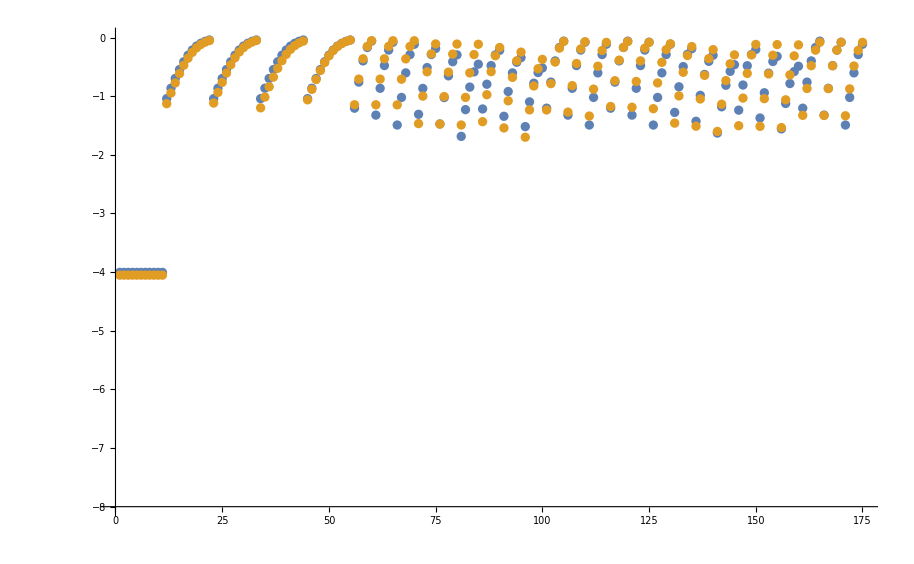

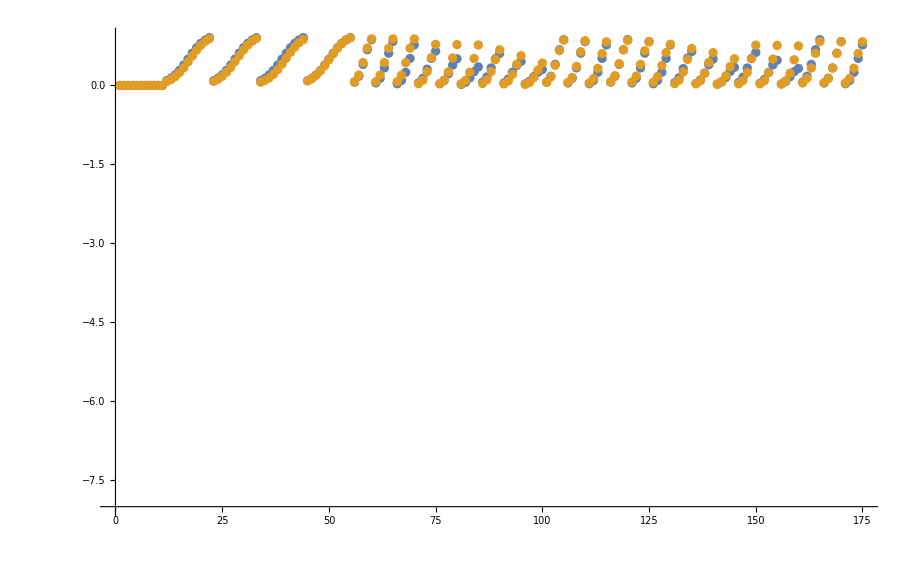

```mathematica
datasetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

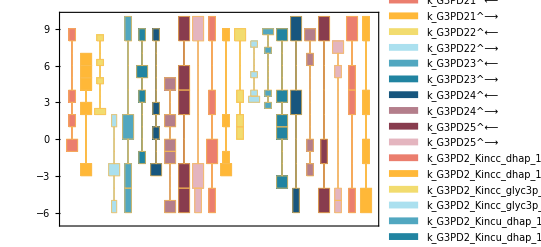

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

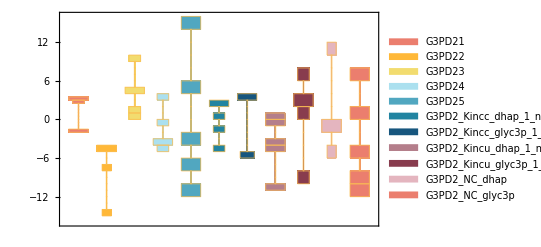

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

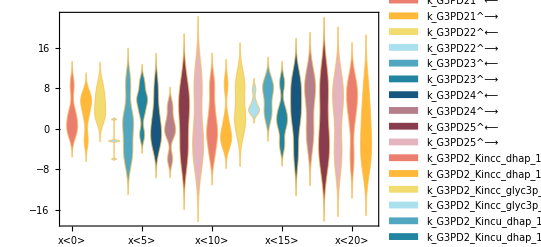

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

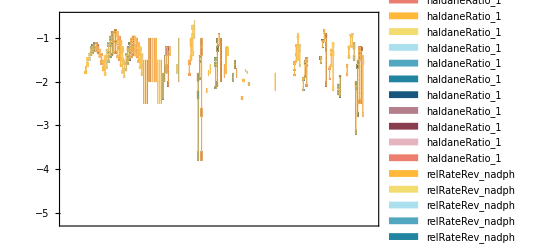

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
3.4×10^-6 | 4.21702×10^-6 | 24.0301
0.00018 | 0.000217068 | 20.5935
0.000165 | 0.000243954 | 47.8511
0.00003 | 0.0000315779 | 5.25951

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.000099 | 0.0000888953 | 10.2067

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.000099 | 0.0000888953 | 10.2067

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %
4.2×10^-6 | 0.00107852 | 25579.1
2.5×10^-6 | 0.000114266 | 4470.62
0.0013 | 0.00162829 | 25.2531
0.000187 | 0.000883081 | 372.236
0.000038 | 0.000610486 | 1506.54
0.00012 | 0.000610486 | 408.738
6.×10^-7 | 0.000013192 | 2098.67
4.×10^-7 | 0.0000325915 | 8047.87

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %
6.5×10^-6 | 4.95552 | 7.62386×10^7
0.0013 | 0.00297802 | 129.079
0.00024 | 0.000610198 | 154.249
8.×10^-7 | 218.324 | 2.72906×10^10

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

-Graphics-